# Construction of the LS method for the Duffiing Van Der Pol Oscillato.

```mathematica
a1[x_,y_]:=1;
b1[x_,y_]:=0;
a2[x_,y_]:=-α-x^2;
b2[x_,y_]:=-x^2*(x-β);
```

```mathematica
h:=.01;
α:=-0.5;
β:=0.5;
Fh1[x_,y_]:=x+h*y;
Fh2[x_,y_]:=y*Exp[h*a2[x,y]] + b2[x,y]*(Exp[h*a2[x,y]]-1)/(a2[x,y]);
```

-Graphics3D-

-Graphics-

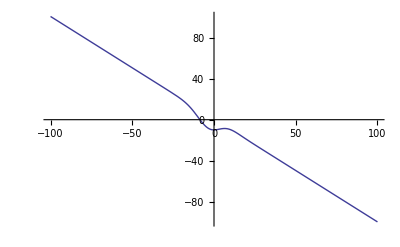

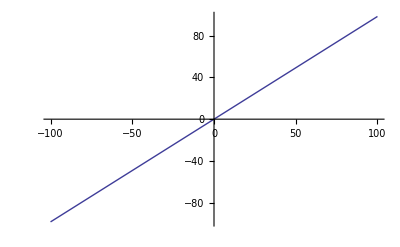

```mathematica
Plot3D[Fh2[x,y],{x,-50,50},{y,-50,50}]
ContourPlot[Fh2[x,y],{x,-50,50},{y,-50,50},PlotLegends->Automatic]
Plot[Fh2[x,-10],{x,-100,100}]
Plot[Fh2[1,y],{y,-100,100}]
```

```mathematica
D[Fh2[x,y],x]
```

-(2 (-1+ⅇ^(-0.5-x^2)) (-0.5+x) x^3)/((-0.5-x^2)^2)-(2 (-1+ⅇ^(-0.5-x^2)) (-0.5+x) x)/(-0.5-x^2)-((-1+ⅇ^(-0.5-x^2)) x^2)/(-0.5-x^2)+(2 ⅇ^(-0.5-x^2) (-0.5+x) x^3)/(-0.5-x^2)-2 ⅇ^(-0.5-x^2) x y